RA Mathematica Problem 1
We are going to play with Mathematica.  Its another “place” where you can write Wolfram Language Code.  Try the following by pressing SHIFT+ENTER on each input line below.

Part One: Plotting Integer Data

Step 1:  Let’s ask Mathematica to make a list of 10 random numbers: (Click on the cell below and press SHIFT+ENTER)

```mathematica
myList = RandomInteger[10,10]
```

{7,7,5,0,0,10,9,8,2,0}

Step 2:  Notice how we stored these 10 values into something named myList This means we can recall those values at any time by simply typing myList  

Try it:

```mathematica
myList
```

{7,7,5,0,0,10,9,8,2,0}

Step 3:  Let’s plot the data and explore different PlotTheme options we can use to look at the data. (Run each of the commands below)

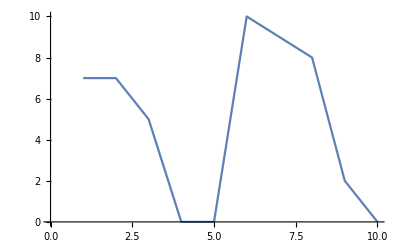

```mathematica
ListLinePlot[myList]
```

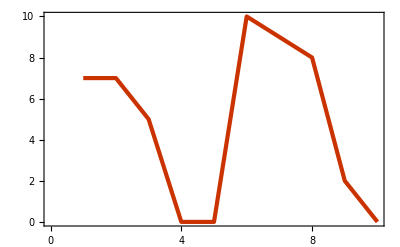

```mathematica
ListLinePlot[myList,PlotTheme->"Web"]
```

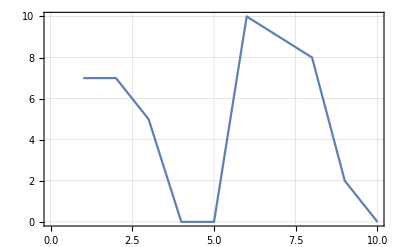

```mathematica
ListLinePlot[myList,PlotTheme->"Detailed"]
```

```mathematica
ListLinePlot[myList,PlotTheme->"Marketing"]
```

-Graphics-

Part Two: Plotting Map Data

Step 1:  Let’s get real geographical data from the internet via Wolfram Alpha.

```mathematica
GeoListPlot[LinguisticAssistant]
```

-Graphics-

Step 2: Let’s zoom out so we can see a larger area:

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

Step 3:  Let’s zoom out a bit more...

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->All]
```

-Graphics-

Step 4:  We can change the GeoBackground too:

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant,GeoBackground->"ReliefMap"]
```

-Graphics-

Part Three: Explore Sample Data

Mathematica includes lots of data of various types.  We’re going to explore that dataset a bit.


Step 1: Lear more about the data that is included in ExampleData[]

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

Step 2: Pick a type you’d like to explore more deeply. I’m choosing “Geometry3D”

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

Step 3: Choose an 3D object you’d like to interact with.  I’m choosing  “Seashell”

```mathematica
ExampleData[{"Geometry3D","Seashell"}]
```

-Graphics3D-

```mathematica
myGraduationDate= LinguisticAssistant
```

```mathematica
WolframAlpha["How many minutes until June 16, 2020?"]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha["What's the average number of breaths per day?"]
```

WolframAlphaQueryResults

```mathematica
1.915×10^6*18
```

3.447×10^7